```mathematica
Needs["AffinityPropagation3`","affinityPropagationPackage3.m"];
Needs["SpectralClustering`","spectralClusteringPackage.m"];
Needs["MolecularCogs`","molecularCogsPackage.m"];
Needs["ErrorBarPlots`"]



(*{p1,p2,p3,p4,p5,p6,p7,p8}=plotListPlotAndStripe["non-bonded","nbd",textSize,72*imageSize];
{p1,p2,p3,p4,p5,p6,p7,p8}=plotListPlotAndStripe["all","total",textSize,72*imageSize];
{p1,p2,p3,p4,p5,p6,p7,p8}=plotListPlotAndStripe["conf","conf",textSize,72*imageSize];
{p1,p2,p3,p4,p5,p6,p7,p8}=plotListPlotAndStripe["bonds","bond",textSize,72*imageSize];
{p1,p2,p3,p4,p5,p6,p7,p8}=plotListPlotAndStripe["vdw","vdw",textSize,72*imageSize];
{p1,p2,p3,p4,p5,p6,p7,p8}=plotListPlotAndStripe["ele","ele",textSize,72*imageSize];*)
```

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{"whichAtomsForDih    1", 5, 6, 7}].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{"whichAtomsForAux    2", 1, 5, "6     # atom numbers forming the auxiliary dihedral angle"}].

```mathematica
(* *)
```

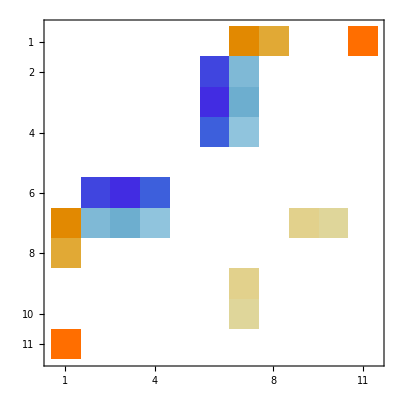

{0.95877,{1,-1,-1,-1,-1,1,1,1,1,1}}

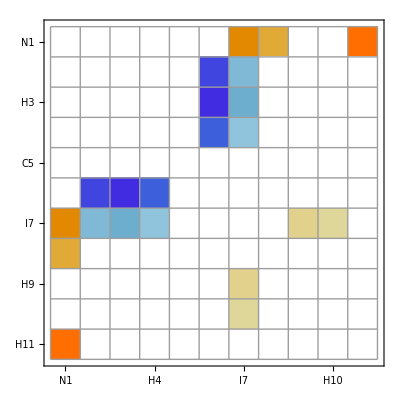

myMatrixPlotWithNumbers[{{0.,0.,0.,0.,0.,-1.17717,-0.799707,0.,0.,-1.76047},{0.,0.,0.,0.,1.36814,0.0585513,0.,0.,0.,0.},{0.,0.,0.,0.,1.37584,0.0595368,0.,0.,0.,0.},{0.,0.,0.,0.,1.35594,0.0582224,0.,0.,0.,0.},{0.,1.36814,1.37584,1.35594,0.,0.,0.,0.,0.,0.},{-1.17717,0.0585513,0.0595368,0.0582224,0.,0.,0.,-0.00706402,-0.00140173,0.},{-0.799707,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.00706402,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.00140173,0.,0.,0.,0.},{-1.76047,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{1,2,3,4,5,6,7,8,9,10}]

```mathematica
textSize=20;

interaction="non-bonded";
max="-62.50";
min="-172.50";
{angles,mats,varMats,diff}=getMatsFromInterval[max,min,interaction];
{mat,varMat}=meanForInterval[mats,varMats,diff];
MatrixPlot[mat]

{packedMat,which}=packMatrix[mat];
myResults=geneticClustering[packedMat,10,200]

(*{whichLeft,whichRight}=Flatten[Position[myResults⟦2⟧,#]]&/@{1,-1}
0.5*Total[Total[packedMat⟦whichLeft,whichLeft⟧]]
0.5*Total[Total[packedMat⟦whichRight,whichRight⟧]]
Total[Total[packedMat⟦whichLeft,whichRight⟧]]
plotBlockLikeSimMat[myResults⟦2⟧,packedMat]
score[myResults⟦2⟧,myResults⟦2⟧]*)
myMatrixPlot[mat,Range[Length[mat]],textSize]
myMatrixPlotWithNumbers[-packedMat,Range[Length[packedMat]],textSize]
```

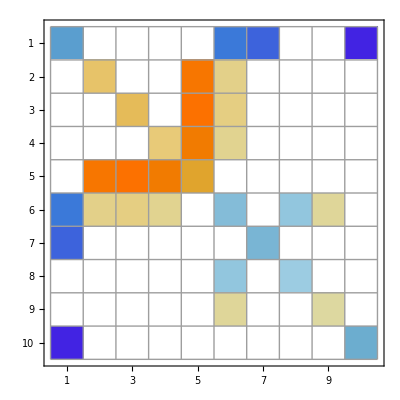

```mathematica
myMatrixPlotWithNumbers[-packedMat+DiagonalMatrix[Mean/@-packedMat],Range[Length[packedMat]],textSize]
```

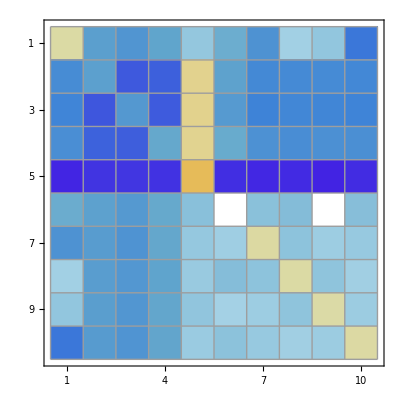

```mathematica
myMatrixPlotWithNumbers[Total@affinityPropagation2andAHalf[-packedMat,0.5,2],Range[Length[mat]],textSize]
```

```mathematica
interaction="tors";
prefix="tors";
{mats,accumulatedMat}=extractAccumulatedMat[max,min,interaction];
mat=accumulatedMat⟦All,All,1,-1⟧;
{packedMat,which}=packMatrix[mat];
myResults=geneticClustering[packedMat,10,200];
unpackedClustering=unpackClustering[myResults⟦2⟧,which,Length[mat]];
```

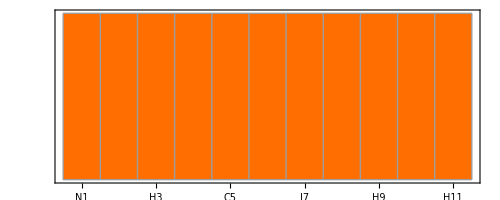

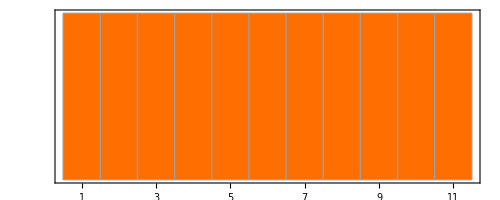

```mathematica
{reverseGear,forwardGear}=Flatten[Position[unpackedClustering,#]]&/@{-1,1};
MatrixPlot[{unpackedClustering},FrameTicks->{None,{Range[Length[ATOMS]],ATOMS}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Directive[Opacity[1],Bold,Black,16],Mesh->True]
MatrixPlot[{unpackedClustering},FrameTicks->{None,{Range[Length[ATOMS]],NUMBERS}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Directive[Opacity[1],Bold,Black,16],Mesh->True]
```

Transpose::nmtx: The first two levels of the one-dimensional list {{-179., -178.5, -178., -177.5, -177., -176.5, -176., -175.5, -175., -174.5, -174., -173.5, -173., -172.5, -172., -171.5, -171., -170.5, -170., -169.5, -169., -168.5, -168., -167.5, -167., -166.5, -166., -165.5, -165., -164.5, -164., -163.5, -163., -162.5, -162., -161.5, -161., -160.5, -160., -159.5, -159., -158.5, -158., -157.5, -157., -156.5, -156., -155.5, -155., -154.5, « 189 »}, {0.0696844, 0.0708086, 0.0785889, « 45 », 0.132225, 0.130972, « 171 »}} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {{-179., -178.5, -178., -177.5, -177., -176.5, -176., -175.5, -175., -174.5, -174., -173.5, -173., -172.5, -172., -171.5, -171., -170.5, -170., -169.5, -169., -168.5, -168., -167.5, -167., -166.5, -166., -165.5, -165., -164.5, -164., -163.5, -163., -162.5, -162., -161.5, -161., -160.5, -160., -159.5, -159., -158.5, -158., -157.5, -157., -156.5, -156., -155.5, -155., -154.5, « 189 »}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 23 », 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 171 »}} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {{-179., -178.5, -178., -177.5, -177., -176.5, -176., -175.5, -175., -174.5, -174., -173.5, -173., -172.5, -172., -171.5, -171., -170.5, -170., -169.5, -169., -168.5, -168., -167.5, -167., -166.5, -166., -165.5, -165., -164.5, -164., -163.5, -163., -162.5, -162., -161.5, -161., -160.5, -160., -159.5, -159., -158.5, -158., -157.5, -157., -156.5, -156., -155.5, -155., -154.5, « 189 »}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 171 »}} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

-Graphics-

torsDerivative.pdf

Part::partw: Part 222 of {0., 0.0351232, 0.0724726, 0.11173, 0.151623, 0.192675, 0.234753, 0.277437, 0.320965, 0.366737, 0.41349, 0.460712, 0.508746, « 25 », 2.0876, 2.15571, 2.22367, 2.29062, 2.35921, 2.42627, 2.49213, 2.55816, 2.62346, 2.68833, 2.75326, 2.81906, « 171 »} does not exist.

Part::partw: Part 222 of {0., 1.35974×10^-7, 2.67809×10^-7, 3.92872×10^-7, 5.10384×10^-7, 6.22706×10^-7, 7.51099×10^-7, 9.01194×10^-7, 1.05788×10^-6, 1.21018×10^-6, 1.34621×10^-6, 1.47052×10^-6, 1.60623×10^-6, « 25 », 5.30492×10^-6, 5.43906×10^-6, 5.58015×10^-6, 5.73723×10^-6, 5.88191×10^-6, 6.0236×10^-6, 6.15792×10^-6, 6.2737×10^-6, 6.39084×10^-6, 6.51348×10^-6, 6.63648×10^-6, 6.75957×10^-6, « 171 »} does not exist.

Part::partw: Part 223 of {0., 0.0351232, 0.0724726, 0.11173, 0.151623, 0.192675, 0.234753, 0.277437, 0.320965, 0.366737, 0.41349, 0.460712, 0.508746, « 25 », 2.0876, 2.15571, 2.22367, 2.29062, 2.35921, 2.42627, 2.49213, 2.55816, 2.62346, 2.68833, 2.75326, 2.81906, « 171 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

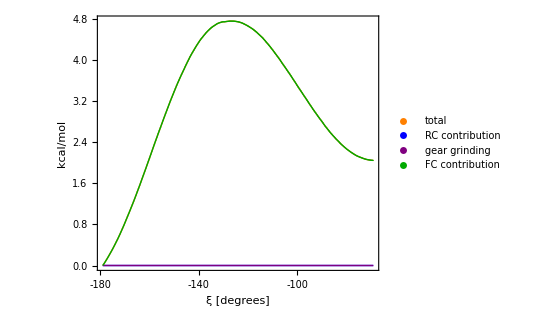

torsPMF.pdf

```mathematica
textSize=20;
{forwardPull,reversePull,gearGrinding,totalPull}=extractGearPMF[mats,forwardGear,reverseGear];

upperLimit=Max[Flatten[{forwardPull⟦1,All⟧,reversePull⟦1,All⟧,gearGrinding⟦1,All⟧}]];
lowerLimit=Min[Flatten[{forwardPull⟦1,All⟧,reversePull⟦1,All⟧,gearGrinding⟦1,All⟧}]];
step=(upperLimit-lowerLimit)/4;
ticks=Range[lowerLimit-step,upperLimit+step,step];
ListPlot[{{Range[-179,-60,0.5],forwardPull⟦1,All⟧}ᵀ,{Range[-179,-60,0.5],reversePull⟦1,All⟧}ᵀ,{Range[-179,-60,0.5],gearGrinding⟦1,All⟧}ᵀ,{Range[-179,-60,0.5],totalPull⟦1,All⟧}ᵀ},PlotLegends->Placed[PointLegend[{Style["FGC",Bold,textSize],Style["RGC",Bold,textSize],Style["GG",Bold,textSize],Style["total",Bold,textSize]},LegendMarkerSize->16,LegendMarkers->"Filled"],Above],Joined->True,PlotRange->All,PlotStyle->Thick,Frame->{{True,False},{True,False}},FrameLabel->{Style["ξ [degrees]",Bold,textSize],Style["kcal/mol",textSize,Bold]},FrameTicks->{{Automatic,None},{{-180,-160,-140,-120,-100,-80,-60},None}},LabelStyle->Directive[Black,textSize-2,Bold],AspectRatio->0.8]
Export[prefix<>"Derivative.pdf",%,"PDF"]

{forwardPull,reversePull,gearGrinding,totalPull}=extractGearPMF[accumulatedMat,forwardGear,reverseGear];
ErrorListPlot[prepareForErrorListPlot/@{forwardPull,reversePull,gearGrinding,totalPull},PlotLegends->Placed[PointLegend[{Style["total",Bold,textSize],Style["RC contribution",Bold,textSize],Style["gear grinding",Bold,textSize],Style["FC contribution",Bold,textSize]},LegendMarkerSize->16,LegendMarkers->"Filled"],Above],Joined->True,PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{Style["ξ [degrees]",Bold,textSize],Style["kcal/mol",textSize,Bold]},PlotStyle->{Orange,Blue,Purple,Darker[Green]},FrameTicks->{{Automatic,None},{{-180,-160,-140,-120,-100,-80,-60},None}},LabelStyle->Directive[Black,textSize-2,Bold],AspectRatio->0.8]
Export[prefix<>"PMF.pdf",%,"PDF"]
```

```mathematica
textSize=20;


ListPlot[{ToExpression/@DIHEDRALS,Table[clusteringSimilarity[unpackedClustering,wyniki⟦All,2⟧⟦i⟧,Length[ATOMS]],{i,1,Length[wyniki⟦All,2⟧]}]}ᵀ,Joined->True,Frame->True,FrameLabel->{Style["ξ [degrees]",Bold,textSize],Style["SIMILARITY",textSize,Bold]},LabelStyle->Directive[Black,textSize-2,Bold],PlotStyle->Thick,PlotRange->{All,{-1,1}},Filling->Bottom]
```

-Graphics-

{0.413187,{1,1,1,1,1,1,1,1,1,1,1}}

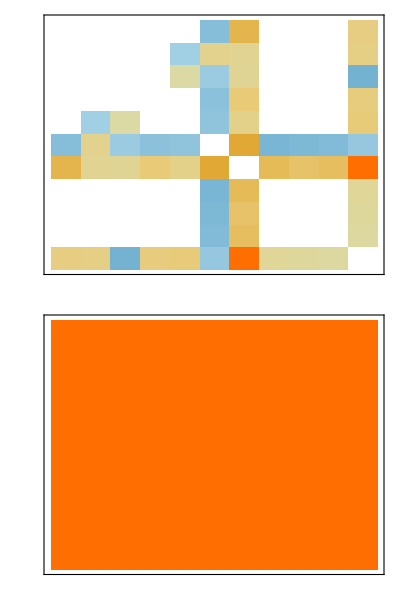

```mathematica
mat=accumulatedMat⟦All,All,1,-1⟧;
{packedMat,which}=packMatrix[mat];
myResults=geneticClustering[packedMat,10,200]
unpackedClustering=unpackClustering[myResults⟦2⟧,which,Length[mat]];
{reverseGear,forwardGear}=Flatten[Position[unpackedClustering,#]]&/@{-1,1};
plotBlockLikeSimMat[unpackedClustering+2,mat,72*3]
```

```mathematica
interaction="ele";
prefix="ele";
{mats,accumulatedMat}=extractAccumulatedMat[max,min,interaction];
mat=accumulatedMat⟦All,All,1,-1⟧;
{packedMat,which}=packMatrix[mat];
myResults=geneticClustering[packedMat,10,200];
unpackedClustering=unpackClustering[myResults⟦2⟧,which,Length[mat]];
```

{9,6,4,3,2,5,11,10,8,7,1}

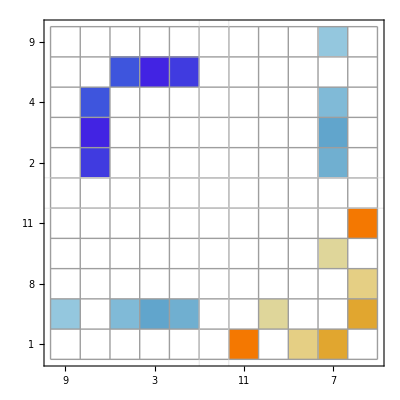

```mathematica
map=Sort[Range[1,Length[mat]],unpackedClustering[[#1]]<unpackedClustering[[#2]]&]
If[Length[Flatten[Position[unpackedClustering,0]]]==0,
zeroLeftPosition=Min[Flatten[Position[unpackedClustering⟦map⟧,1]]];
MatrixPlot[mat⟦map,map⟧,FrameTicks->{{Range[Length[ATOMS[[map]]]],ATOMS[[map]]}ᵀ,{Range[Length[ATOMS[[map]]]],Rotate[#,90 Degree]&/@ATOMS[[map]]}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Directive[Opacity[1],Bold,Black,16],Mesh->All,GridLines->{{zeroLeftPosition-1},{Length[ATOMS]-zeroLeftPosition+1}},GridLinesStyle->{Directive[Thick,Black],Directive[Thick,Black]},Method->{"GridLinesInFront"->True}]
,
{zeroLeftPosition,zeroRightPosition}=#[Flatten[Position[unpackedClustering,0]]]&/@{Min,Max};
{zeroLeftPosition,zeroRightPosition}={zeroLeftPosition,zeroRightPosition}+1;
MatrixPlot[mat⟦map,map⟧,FrameTicks->{{Range[Length[ATOMS[[map]]]],NUMBERS[[map]]}ᵀ,{Range[Length[ATOMS[[map]]]],Rotate[#,0 Degree]&/@NUMBERS[[map]]}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Directive[Opacity[1],Bold,Black,16],Mesh->All,GridLines->{{zeroLeftPosition-1,zeroRightPosition},{Length[ATOMS]-zeroLeftPosition+1,Length[ATOMS]-zeroRightPosition}},GridLinesStyle->{Directive[Thick,Black],Directive[Thick,Black]},Method->{"GridLinesInFront"->True}]
]

(*,FrameTicks->{{Range[Length[ATOMS[[map]]]],ATOMS[[map]]}ᵀ,{Range[Length[ATOMS[[map]]]],ATOMS[[map]]}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],Mesh->All,GridLines->{{3,7},{4,8}},GridLinesStyle->{Directive[Thick,Black],Directive[Thick,Black]},Method->{"GridLinesInFront"->True}]*)
```

```mathematica
max="-60.00";
min="-179.00";
freeEnergy=extractPMF[max,min,1]ᵀ;
freeEnergy={freeEnergy⟦1⟧,#^2&/@freeEnergy⟦2⟧};
entropy=extractPMF[max,min,3]ᵀ;
entropy={entropy⟦1⟧,#^2&/@entropy⟦2⟧};
energy={freeEnergy⟦1⟧-entropy⟦1⟧,freeEnergy⟦2⟧+entropy⟦2⟧};
```

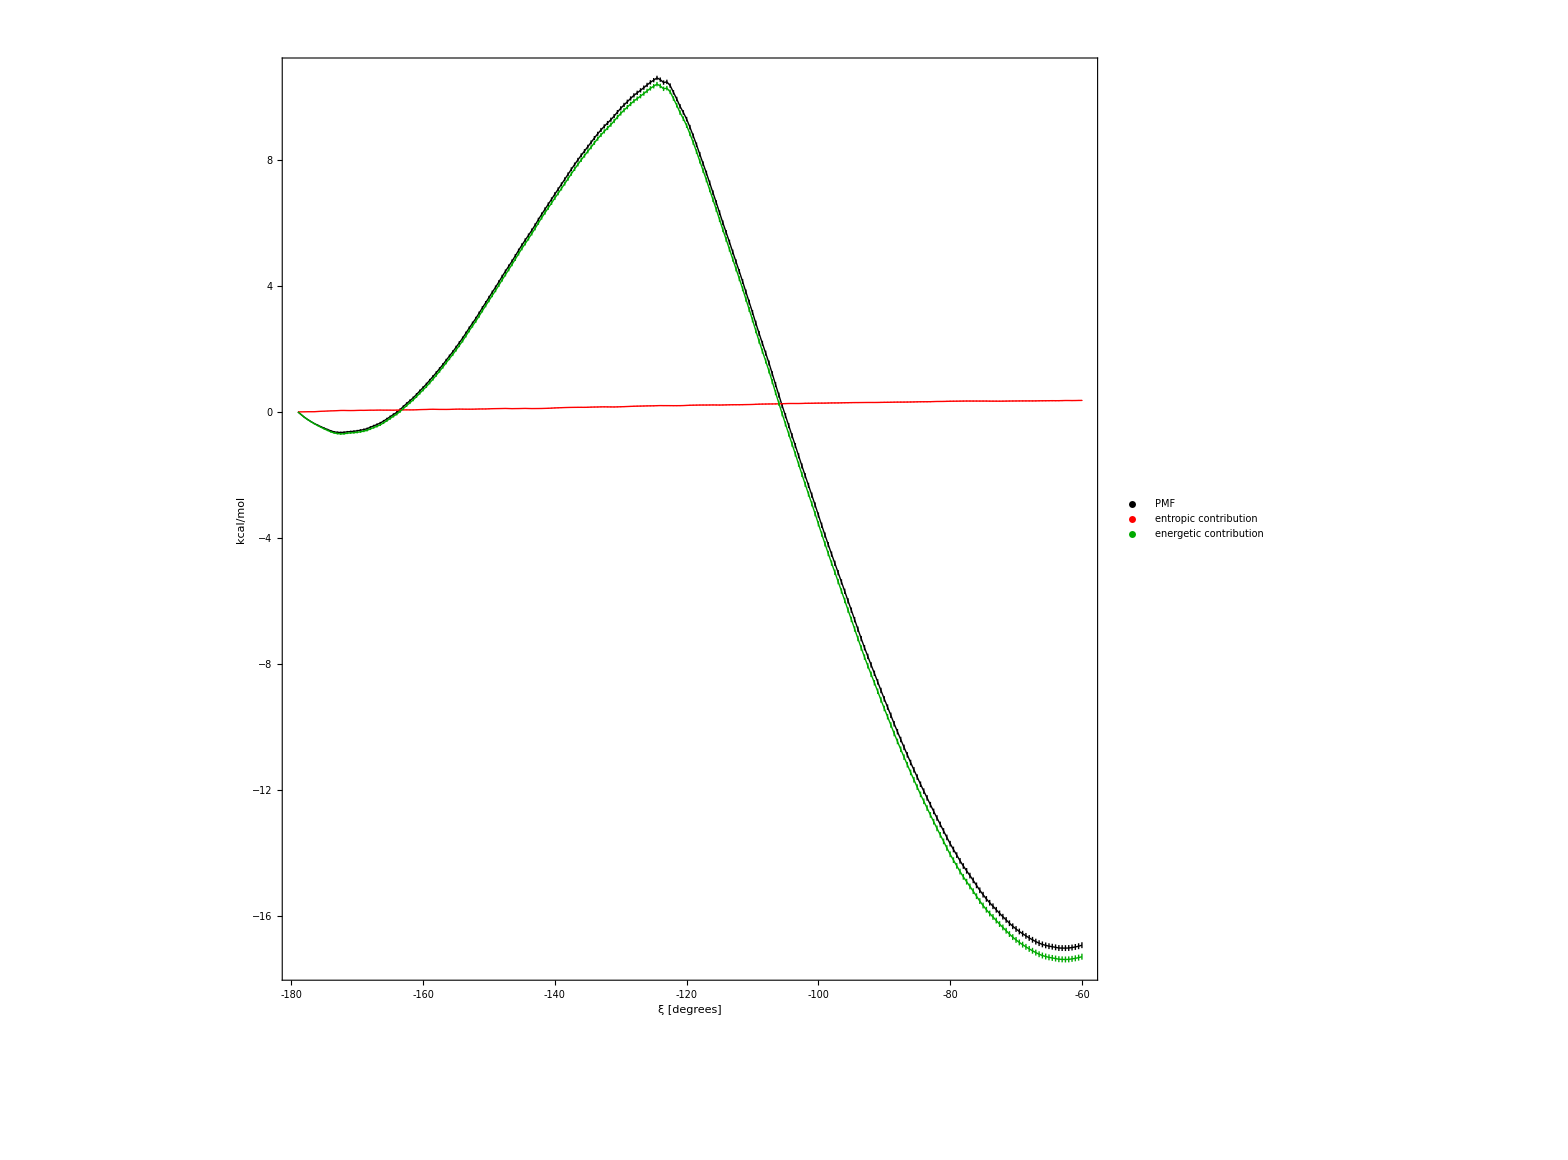

```mathematica
textSize=20;
g=ErrorListPlot[prepareForErrorListPlot[trapezoidalIntegration[#,0.5]]&/@{freeEnergy,entropy,energy},PlotLegends->Placed[PointLegend[{Style["PMF",Bold,textSize-6,FontFamily->"Helvetica"],Style["entropic\ncontribution",Bold,textSize-6,FontFamily->"Helvetica"],Style["energetic\ncontribution",Bold,textSize-6,FontFamily->"Helvetica"]},LegendMarkerSize->textSize-6,LegendMarkers->"Filled",LegendLayout->"Row"],Top],Joined->True,PlotRange->All,PlotStyle->{Black,Red,Darker[Green]},Frame->{{True,False},{True,False}},FrameLabel->{Style["ξ [degrees]",Bold,textSize,FontFamily->"Helvetica"],Style["kcal/mol",textSize,Bold,FontFamily->"Helvetica"]},FrameTicks->{{Automatic,None},{{-180,-160,-140,-120,-100,-80,-60},None}},LabelStyle->Directive[Black,textSize-6,Bold],TicksStyle->Directive[Bold,FontFamily->"Helvetica",textSize-6],AspectRatio->.9,ImageSize->72*4.5]
Export["realPMF.eps",%,"EPS"];
```

```mathematica
a=Import["angle-150_measured_1450x2000.png","PNG"];
b=Import["angle-90_measured_1550x2000.png","PNG"];
c=Import["angle-60_measured_2100x1400.png","PNG"];
(*{a,b,c}=ImageCrop/@{a,b,c};*)
c=ImageCrop[c];
g=Import["realPMF.pdf","PDF"]⟦1⟧
```

{-Graphics-}

```mathematica
Export["grid.eps",GraphicsGrid[{{a,c},{b,g}},ImageSize->72*6.5],"EPS",ImageResolution->1200]
```

grid.eps

-Graphics-

```mathematica
grafik=Labeled[MatrixPlot[{{1,1,1,1,1,1,2,1,1,1,1}},ImageSize->72*4],"asd",Top,ImageSize->72*4];
Export["grafik.pdf",grafik,"PDF",ImageSize->72*4]
```

grafik.pdf